### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->10,U1->0,U2->0(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->S1,S2->S2,S3->0,S4->0,S5->0,S6->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[10-j297]&&NonNegative[j297]&&NonNegative[10-j297]&&NonNegative[j297]&&NonNegative[10-jt310]&&NonNegative[jt310]&&NonNegative[-j297+jt310]&&NonNegative[j297-jt310]&&NonNegative[j297-jt310]&&NonNegative[-j297+jt310]&&NonNegative[10-j297]&&NonNegative[j297]&&NonNegative[10+S2-u319+u320]&&NonNegative[10+S1-u319+u321]&&NonNegative[-10+u319-u320]&&NonNegative[-u320+u321]&&NonNegative[-10+u319-u321]&&NonNegative[u320-u321]&&NonNegative[10-j297-u320]&&NonNegative[j297-u321]&&(10-jt310==0||-j297+jt310==0)&&(jt310==0||j297-jt310==0)&&(j297-jt310==0||-j297+jt310==0)&&(10-jt310==0||10+S2-u319+u320==0)&&(jt310==0||10+S1-u319+u321==0)&&(-j297+jt310==0||-10+u319-u320==0)&&(j297-jt310==0||-u320+u321==0)&&(j297-jt310==0||-10+u319-u321==0)&&(-j297+jt310==0||u320-u321==0)&&(10-j297==0||10-j297-u320==0)&&(j297==0||j297-u321==0)
and the rules are:
<|j300→10,u328→0,u329→0,j295→10,j296→10-j297,j298→10-j297,j299→j297,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,jt307→0,jt308→10,jt309→10-jt310,jt311→-j297+jt310,jt312→j297-jt310,jt313→j297-jt310,jt314→-j297+jt310,jt315→10-j297,jt316→0,jt317→j297,jt318→0,u322→0,u323→0,u325→-10+u319,u326→-10+j297+u320,u327→-j297+u321,u330→u319,u324→u319|>

DataToEquations: The system is:
u319≥15&&u321==5&&u320==5&&10+S2+u320==u319&&10+S1==S2+2 u320&&jt310+u320==10&&j297==jt310
and the rules are:
<|j300→10,u328→0,u329→0,j295→10,j296→10-j297,j298→10-j297,j299→j297,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,jt307→0,jt308→10,jt309→10-jt310,jt311→-j297+jt310,jt312→j297-jt310,jt313→j297-jt310,jt314→-j297+jt310,jt315→10-j297,jt316→0,jt317→j297,jt318→0,u322→0,u323→0,u325→-10+u319,u326→-10+j297+u320,u327→-j297+u321,u330→u319,u324→u319|>

DataToEquations: It took 0.056607 seconds to reduce with NewReduce!

DataToEquations: Possible multiple solutions 
{S1≥0,<|j300→10,u328→0,u329→0,j295→10,j296→10-5,j298→10-5,j299→5,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,jt307→0,jt308→10,jt309→10-5,jt311→-5+5,jt312→5-5,jt313→5-5,jt314→-5+5,jt315→10-5,jt316→0,jt317→5,jt318→0,u322→0,u323→0,u325→-10+(15+S1),u326→-10+5+5,u327→-5+5,u330→15+S1,u324→15+S1,j297→5,jt310→5,S2→S1,u319→15+S1,u320→5,u321→5|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.074503,Null}

<|{1,1->2}→15+S1,{1,en292->1}→15+S1,{2,1->2}→5+S1,{2,2->3}→5,{2,2->4}→5,{3,2->3}→0,{3,3->ex293}→0,{4,2->4}→0,{4,4->ex294}→0,{en292,en292->1}→15+S1,{ex293,3->ex293}→0,{ex294,4->ex294}→0|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[2-j289]&&NonNegative[j289]&&NonNegative[2-j289]&&NonNegative[j289]&&NonNegative[2-jt302]&&NonNegative[jt302]&&NonNegative[-j289+jt302]&&NonNegative[j289-jt302]&&NonNegative[j289-jt302]&&NonNegative[-j289+jt302]&&NonNegative[2-j289]&&NonNegative[j289]&&NonNegative[2-u311+u312]&&NonNegative[2-u311+u313]&&NonNegative[-2+u311-u312]&&NonNegative[-u312+u313]&&NonNegative[-2+u311-u313]&&NonNegative[u312-u313]&&NonNegative[7-j289-u312]&&NonNegative[1+j289-u313]&&(2-jt302==0||-j289+jt302==0)&&(jt302==0||j289-jt302==0)&&(j289-jt302==0||-j289+jt302==0)&&(2-jt302==0||2-u311+u312==0)&&(jt302==0||2-u311+u313==0)&&(-j289+jt302==0||-2+u311-u312==0)&&(j289-jt302==0||-u312+u313==0)&&(j289-jt302==0||-2+u311-u313==0)&&(-j289+jt302==0||u312-u313==0)&&(2-j289==0||7-j289-u312==0)&&(j289==0||1+j289-u313==0)
and the rules are:
<|j292→2,u320→5,u321→1,j287→2,j288→2-j289,j290→2-j289,j291→j289,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→2,jt301→2-jt302,jt303→-j289+jt302,jt304→j289-jt302,jt305→j289-jt302,jt306→-j289+jt302,jt307→2-j289,jt308→0,jt309→j289,jt310→0,u314→5,u315→1,u317→-2+u311,u318→-2+j289+u312,u319→-j289+u313,u322→u311,u316→u311|>

DataToEquations: It took 0.03768 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.055495,Null}

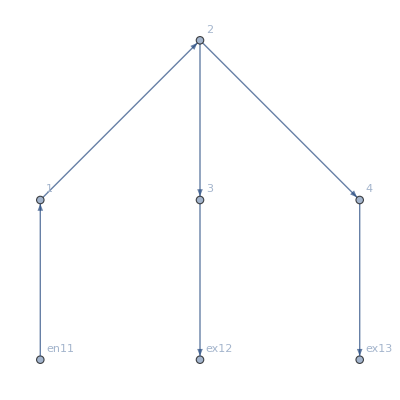

<|{1,1->2}→u506,{1,en479->1}→u506,{2,1->2}→-1+u506,{2,2->3}→u507,{2,2->4}→u508,{3,2->3}→-1+j484+u507,{3,3->ex480}→5,{4,2->4}→-j484+u508,{4,4->ex481}→1,{en479,en479->1}→u506,{ex480,3->ex480}→5,{ex481,4->ex481}→1|>

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]](*//KeySort*)
```

<|j253→2,u281→5,u282→1,j248→2,j249→0,j251→0,j252→2,j254→0,j255→0,j256→0,j257→0,j258→0,j259→0,jt260→0,jt261→2,jt262→0,jt264→0,jt265→0,jt266→0,jt267→0,jt268→0,jt269→0,jt270→2,jt271→0,u275→5,u276→1,u278→3,u279→3,u280→1,u283→5,u277→5,j250→2,jt263→2,u272→5,u273→3,u274→3|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```